# Precision of morphogen - driven tissue patterning during development is enhanced through contact - mediated cellular interactions

Chandrashekar Kuyyamudi^(1,2), Shakti N. Menon^1, and Sitabhra Sinha^(1,2)

^1 The Institute of Mathematical Sciences, CIT Campus, Taramani, Chennai 600113, India
^2 Homi Bhabha National Institute, Anushaktinagar, Mumbai 400 094, India

## Steady states for a single cell and a pair of coupled cells

Our model is described by the following set of equations:

ⅆA/ⅆt=α_A ℋ_h(M,K_1)ℋ_h'(B,K_3)Φ_A+γ_A ℋ_g(S,Q)-A/τ_A,
ⅆB/ⅆt=α_B ℋ_h(M,K_2)ℋ_h'(A,K_4)Φ_B+γ_B ℋ_g(S,Q)-B/τ_B,
ⅆR/ⅆt=β_R0+β_R ℋ_g(A,J)ℋ_g(B_i,J)-k_tr R L_tr-R/τ_R,
ⅆL/ⅆt=β_L0+β_L ℋ_g'(S,K_5)-k_tr R_tr L-L/τ_L,
ⅆS/ⅆt=k_tr R L_tr-S/τ_S,
ⅆM/ⅆt=α_M δ_(i,1)-D_M∇^2 M-M/τ_M,

where

ℋ_β(X,C)=X^β/(X^β+C^β)  and  ℋ_β'(X,C)=C^β/(X^β+C^β).

We consider the coupling type in which S represses B (see manuscript for details). In this case, we have:

Φ_A=1, Φ_B=Q^g/(Q^g+S^g),γ_A=0,γ_B=0.

The steady state value of the morphogen concentration (M) at each cell can be obtained from the solution of the equation:

ⅆM/ⅆt=α_M δ_(i,1)-D_M∇^2 M-M/τ_M.

Note that M is only produced at a single cell, namely at i=1. Considering a spatially extended array of n(=50) cells, and setting D_M=50 and α=25000, we obtain the following steady state values for M:

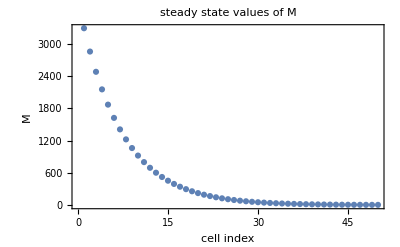

```mathematica
τM=1; (* mean lifetime of M *)
DM=50; (* diffusion coefficient *)
αM=25000; (* production rate *)
n = 50; (* number of cells *)
tmax =1000; (* duration of simulation *)

vars = Table[Subscript[x, i][t], {i,1,n}]; (* define a list of variables for the n cells *)

(* equation for the cell at the left boundary *)
eqnL={Subscript[x, 1]'[t]==DM (Subscript[x, 2][t]-Subscript[x, 1][t])-(Subscript[x, 1][t])/τM+αM,Subscript[x, 1][0]==0};
(* equations for the cells in the middle *)
eqnM=Table[{Subscript[x, i]'[t]==DM (Subscript[x, i+1][t]-2 Subscript[x, i][t]+Subscript[x, i-1][t])-(Subscript[x, i][t])/τM,Subscript[x, i][0]==0},{i,2,n-1}];
(* equation for the cell at the right boundary *)
eqnR={Subscript[x, n]'[t]==DM (Subscript[x, n-1][t]-Subscript[x, n][t])-(Subscript[x, n][t])/τM,Subscript[x, n][0]==0};

eqns={};
AppendTo[eqns,eqnL];
For[i=1,i<n-1,i++,AppendTo[eqns,eqnM[[i]]];]
AppendTo[eqns,eqnR];

nd=NDSolve[eqns, vars, {t, 0, tmax}];

(* steady state values of the morphogen *)
Mvals=Table[Evaluate[Subscript[x, i][t]/.nd][[1]]/.{t->tmax},{i,1,n}];

ListPlot[Mvals,PlotRange->All,Frame->True,FrameLabel->{"cell index","M"},PlotLabel->"steady state values of M"]
```

Thus, we have an exponential gradient in the concentration of morphogen along the domain. In the following we study fluctuations around the steady state of the system for two scenarios: (i) a single uncoupled cell located at different positions along this morphogen gradient, (ii) a pair of cells that are located at adjacent positions along the gradient. For both cases, the dynamics of each cell i can be described through the following set of equations:

(ⅆ A_i)/ⅆt=α_A(M_i^h/(K_1^h+M_i^h))(K_3^h/(K_3^h+B_i^h))-A_i/τ_A,
(ⅆ B_i)/ⅆt=α_B(M_i^h/(K_2^h+M_i^h))(K_4^h/(K_4^h+A_i^h))(Q^g/(Q^g+S_i^g))-B_i/τ_B,
(ⅆ R_i)/ⅆt=β_R0+β_R(A_i^g/(J^g+A_i^g))(B_i^g/(J^g+B_i^g))-k_tr R_i L_tr-R_i/τ_R,
(ⅆ L_i)/ⅆt=β_L0+β_L(K_5^g/(K_5^g+S_i^g))-k_tr R_tr L_i-L_i/τ_L,
(ⅆ S_i)/ⅆt=k_tr R_i L_tr-S_i/τ_S,
(ⅆ M_i)/ⅆt=α_Mi-M_i/τ_M,

where we have introduced the parameter α_Mi=M_i^ss/τ_M,  and where M_i^ss is the steady state concentration of the morphogen at cell i (described above). By specifying the value of α_Mi, we can hence model the dynamics at different locations along the domain. For the current analysis, we choose the following values for the remaining parameters:

```mathematica
(* production rates *)
αA=2000;αB=2000;βR0=20;βL0=20;βR=200;βL=200;

(* mean lifetimes of molecules *)
τA=0.25;τB=0.25;τR=0.2;τL=0.2;τM=1.0;

(* Hill exponents *)
h=2.0;g=4.0;

(* half-saturation constants *)
K1=50;K2=200;K3=100;K4=200;

(* strength of trans-regulation *)
ktr[τS_]:= 2.0/τS

Shalfmax=2.0*0.5*βR*τR*0.5*0.5*βL*τL;

(* threshold value beyond which S represses D *)
K5=5 *Shalfmax;

(* threshold value beyond which S represses B *)
Q=0.5*Shalfmax;

(* threshold value beyond which A and B upregulate R *)
J=44.67;
```

In the following analysis we shall choose τ_S=2, but similar results can be obtained for a range of τ_S.

We introduce the following functions to define the LHS of the 6 equations :

```mathematica
E1[A_,B_,M_]:=αA(M^h/(K1^h+M^h))(K3^h/(K3^h+B^h))-A/τA

E2[A_,B_,S_,M_]:=αB(M^h/(K2^h+M^h))(K4^h/(K4^h+A^h))(Q^g/(Q^g+S^g))-B/τB

E3[A_,B_,R_,Ltr_,τS_]:=βR0+βR(A^g/(J^g+A^g))(B^g/(J^g+B^g))-ktr[τS] R Ltr-R/τR

E4[L_,S_,Rtr_,τS_]:=βL0+βL(K5^g/(K5^g+S^g))-ktr[τS] Rtr L-L/τL

E5[R_,S_,Ltr_,τS_]:=ktr[τS] R Ltr-S/τS

E6[M_,αM_]:=αM-M/τM
```

For single uncoupled cell the terms involving trans-binding will vanish, i.e. L_tr=R_tr=0. Hence, the concentration of the downstream effector will approach the steady state S=0. Furthermore, in this case we find that the equations for R and L become uncoupled from the rest of the equations. Thus, the set of equations can be reduced to:

(ⅆ A_i)/ⅆt=α_A(M_i^h/(K_1^h+M_i^h))(K_3^h/(K_3^h+B_i^h))-A_i/τ_A
(ⅆ B_i)/ⅆt=α_B(M_i^h/(K_2^h+M_i^h))(K_4^h/(K_4^h+A_i^h))-B_i/τ_B
(ⅆ M_i)/ⅆt=α_Mi-M_i/τ_M

Note that while in principle we can decouple the equation for the morphogen concentration, we shall retain it as the subsequent analysis involves considering fluctuations in the morphogen concentration as well.

The following function describes the steady states of the above system at different locations along the morphogen gradient (where Mss are the steady state values of the morphogen concentration M for all the n cells in the domain):

```mathematica
SSuncoupled[Mss_,tmax_]:=
(
nvars=3; (* each cell is described by 3 variables *)
n=Dimensions[Mss,1][[1]];

(* for storing the steady states at different locations along the gradient *)
Xss=Array[0&,{nvars,n}];

(* the Hill function Q^g/(Q^g+S^g) is not present in the uncoupled system *)
Sval=0;

For[cell=1, cell<n+1, cell++,
αM=Mss[[cell]];

sol=NDSolve[{
A'[t]==E1[A[t],B[t],M[t]],
B'[t]==E2[A[t],B[t],Sval,M[t]],
M'[t]==E6[M[t],αM],
A[0]==0,B[0]==0,M[0]==αM},{A,B,M},{t,0,tmax}];

(* steady state values at each location along the domain *)
Xss[[1]][[cell]]=Evaluate[A[tmax]/.sol][[1]];
Xss[[2]][[cell]]=Evaluate[B[tmax]/.sol][[1]];
Xss[[3]][[cell]]=Evaluate[M[tmax]/.sol][[1]];
];
output=Xss
);
```

A pair of coupled cells can be described by the following set of equations:

(ⅆ A_1)/ⅆt=α_A(M_1^h/(K_1^h+M_1^h))(K_3^h/(K_3^h+B_1^h))-A_1/τ_A
(ⅆ B_1)/ⅆt=α_B(M_1^h/(K_2^h+M_1^h))(K_4^h/(K_4^h+A_1^h))(Q^g/(Q^g+S_1^g))-B_1/τ_B
(ⅆ R_1)/ⅆt=β_R0+β_R(A_1^g/(J^g+A_1^g))(B_1^g/(J^g+B_1^g))-k_tr R_1 L_2-R_1/τ_R
(ⅆ L_1)/ⅆt=β_L0+β_L(K_5^g/(K_5^g+S_1^g))-k_tr R_2 L_1-L_1/τ_L
(ⅆ S_1)/ⅆt=k_tr R_1 L_2-S_1/τ_S
(ⅆ M_1)/ⅆt=α_M1-M_1/τ_M
(ⅆ A_2)/ⅆt=α_A(M_2^h/(K_1^h+M_2^h))(K_3^h/(K_3^h+B_2^h))-A_2/τ_A
(ⅆ B_2)/ⅆt=α_B(M_2^h/(K_2^h+M_2^h))(K_4^h/(K_4^h+A_2^h))(Q^g/(Q^g+S_2^g))-B_2/τ_B
(ⅆ R_2)/ⅆt=β_R0+β_R(A_2^g/(J^g+A_2^g))(B_2^g/(J^g+B_2^g))-k_tr R_2 L_1-R_2/τ_R
(ⅆ L_2)/ⅆt=β_L0+β_L(K_5^g/(K_5^g+S_2^g))-k_tr R_1 L_2-L_2/τ_L
(ⅆ S_2)/ⅆt=k_tr R_2 L_1-S_2/τ_S
(ⅆ M_2)/ⅆt=α_M2-M_2/τ_M

The following function describes the steady states of the above system at different locations along the domain for a specified value of τ_S:

```mathematica
SScoupled[Mss_,τS_,tmax_]:=
(
nvars=6; (* each cell is described by 6 variables *)
n=Dimensions[Mss,1][[1]];

(* for storing the steady states at different locations along the domain *)
Xss=Array[0&,{2*nvars,n-1}];

For[cell=1, cell<n, cell++,
αM1=Mss[[cell]];
αM2=Mss[[cell+1]];

sol=NDSolve[{
A1'[t]==E1[A1[t],B1[t],M1[t]],
B1'[t]==E2[A1[t],B1[t],S1[t],M1[t]],
R1'[t]==E3[A1[t],B1[t],R1[t],L2[t],τS],
L1'[t]==E4[L1[t],S1[t],R2[t],τS],
S1'[t]==E5[R1[t],S1[t],L2[t],τS],
M1'[t]==E6[M1[t],αM1],
A2'[t]==E1[A2[t],B2[t],M2[t]],
B2'[t]==E2[A2[t],B2[t],S2[t],M2[t]],
R2'[t]==E3[A2[t],B2[t],R2[t],L1[t],τS],
L2'[t]==E4[L2[t],S2[t],R1[t],τS],
S2'[t]==E5[R2[t],S2[t],L1[t],τS],
M2'[t]==E6[M2[t],αM2],
A1[0]==0,B1[0]==0,R1[0]==0,L1[0]==0,S1[0]==0,M1[0]==αM1,
A2[0]==0,B2[0]==0,R2[0]==0,L2[0]==0,S2[0]==0,M2[0]==αM2},
{A1,B1,R1,L1,S1,M1,A2,B2,R2,L2,S2,M2},{t,0,tmax}];

Xss[[1]][[cell]]=Evaluate[A1[tmax]/.sol][[1]];
Xss[[2]][[cell]]=Evaluate[B1[tmax]/.sol][[1]];
Xss[[3]][[cell]]=Evaluate[R1[tmax]/.sol][[1]];
Xss[[4]][[cell]]=Evaluate[L1[tmax]/.sol][[1]];
Xss[[5]][[cell]]=Evaluate[S1[tmax]/.sol][[1]];
Xss[[6]][[cell]]=Evaluate[M1[tmax]/.sol][[1]];
Xss[[7]][[cell]]=Evaluate[A2[tmax]/.sol][[1]];
Xss[[8]][[cell]]=Evaluate[B2[tmax]/.sol][[1]];
Xss[[9]][[cell]]=Evaluate[R2[tmax]/.sol][[1]];
Xss[[10]][[cell]]=Evaluate[L2[tmax]/.sol][[1]];
Xss[[11]][[cell]]=Evaluate[S2[tmax]/.sol][[1]];
Xss[[12]][[cell]]=Evaluate[M2[tmax]/.sol][[1]];
];
output=Xss
);
```

The following plot displays the steady states of A and B for a single uncoupled cell located at different positions along the domain:

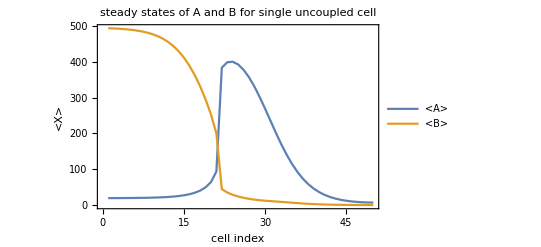

```mathematica
tmax=1000;
Xss0=SSuncoupled[Mvals,tmax];
Lp1=ListPlot[{Xss0[[1]][[All]],Xss0[[2]][[All]]},Joined->True,PlotStyle->{PointSize[0.015],Thick,Thick},Frame->True,FrameLabel->{"cell index","<X>"},PlotLegends->{"<A>","<B>"},PlotLabel->"steady states of A and B for single uncoupled cell"]
```

The following plot displays the steady states of A and B for each of a pair of coupled cells located at different positions along the domain for a specified value of τ_S:

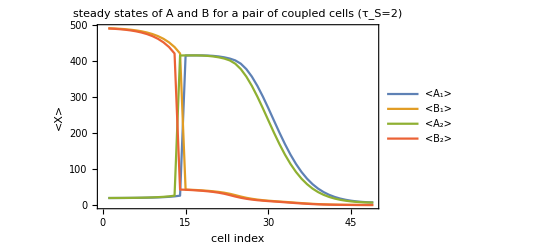

```mathematica
τS=2;
tmax=1000;
Xss1=SScoupled[Mvals,τS,tmax];
Lp2=ListPlot[{Xss1[[1]][[All]],Xss1[[2]][[All]],Xss1[[7]][[All]],Xss1[[8]][[All]]},Joined->True,PlotStyle->{PointSize[0.015],Thick,Thick},Frame->True,FrameLabel->{"cell index","<X>"},PlotLegends->{"<A_1>","<B_1>","<A_2>","<B_2>"},PlotLabel->"steady states of A and B for a pair of coupled cells (τ_S=2)"]
```

## Determining the variance from a linear noise approximation (LNA)

Case I : Single uncoupled cell

We note that the set of equations (3) for an uncoupled cell can effectively be described by the following reactions :

M+B⟶^(r_A^*)M+A+B, A⟶^(1/τ_A)⌀,M+B⟶^(r_B^*)M+B+A, B⟶^(1/τ_B)⌀,⌀⟶^α_M M,M⟶^(1/τ_M)⌀,

where r_A^* and r_B^* represents nonlinear feedback, and the propensities are:

f_1(x)=α_A(M^h/(K1^h+M^h))(K3^h/(K3^h+B^h)),
f_2(x)=A/τ_A,
f_3(x)=α_B(M^h/(K2^h+M^h))(K4^h/(K4^h+A^h)),
f_4(x)=B/τ_B,
f_5(x)=α_M,
f_6(x)=M/τ_M,

and the corresponding Stoichiometric matrix is :

ℳ=(1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1)

We define the following functions to describe the propensities:

```mathematica
f1p[B1_,M1_]:=αA(M1^h/(K1^h+M1^h))(K3^h/(K3^h+B1^h))

f2p[A1_]:=A1/τA

f3p[A1_,B1_,M1_]:=αB(M1^h/(K2^h+M1^h))(K4^h/(K4^h+A1^h))

f4p[B1_]:=B1/τB

f5p[αM_]:=αM

f6p[M1_]:=M1/τM
```

The covariance matrix Σ satisfies the matrix equation

J Σ +Σ J^T=-D

where J is the Jacobian matrix, and the elements D_ij of the diffusion matrix D are defined as follows:

D_ij(x)=∑_(a=1)^N_R ℳ_ia ℳ_ja f_a(x)

where N_R (=6) is the number of reactions. We hence have :

D_11(x)=∑_(a=1)^N_R ℳ_(1a)ℳ_(1a)f_a(x)=ℳ_11^2 f_1(x)+ℳ_12^2 f_2(x),D_12(x)=∑_(a=1)^N_R ℳ_(1a)ℳ_(2a)f_a(x)=0,D_13(x)=∑_(a=1)^N_R ℳ_(1a)ℳ_(3a)f_a(x)=0,
D_21(x)=∑_(a=1)^N_R ℳ_(2a)ℳ_(1a)f_a(x)=0,D_22(x)=∑_(a=1)^N_R ℳ_(2a)ℳ_(2a)f_a(x)=ℳ_23^2 f_3(x)+ℳ_24^2 f_4(x),D_23(x)=∑_(a=1)^N_R ℳ_(2a)ℳ_(3a)f_a(x)=0,
D_31(x)=∑_(a=1)^N_R ℳ_(3a)ℳ_(1a)f_a(x)=0,D_32(x)=∑_(a=1)^N_R ℳ_(3a)ℳ_(2a)f_a(x)=0,D_33(x)=∑_(a=1)^N_R ℳ_(3a)ℳ_(3a)f_a(x)=ℳ_35^2 f_5(x)+ℳ_36^2 f_6(x).

At the fixed point x^*=(A^*,B^*,M^*), we hence have:

D=(f_1(x^*)+f_2(x^*) | 0 | 0
0 | f_3(x^*)+f_4(x^*) | 0
0 | 0 | f_5(x^*)+f_6(x^*))

which we define using the following function:

```mathematica
Df0[f1_,f2_,f3_,f4_,f5_,f6_]:=({{f1+f2, 0, 0}, {0, f3+f4, 0}, {0, 0, f5+f6}})
```

We define the covariance matrix Σ as follows:

```mathematica
Σ0=({{r1c1, r1c2, r1c3}, {r2c1, r2c2, r2c3}, {r3c1, r3c2, r3c3}});
```

Noting that LHS of each of the 3 equations are:

lhs1=α_A(M^h/(K1^h+M^h))(K3^h/(K3^h+B^h))-A/τ_A
lhs2=α_B(M^h/(K2^h+M^h))(K4^h/(K4^h+A^h))-B/τ_B
lhs3=α_M-M/τ_M

we see the Jacobian is:

J_(x^*)=(-1/τ_A | d1B | d1M
d2A | -1/τ_B | d2M
0 | 0 | -1/τ_M),diV=(∂lhsi(x^*))/(∂V)

Using the previously defined functions Ei(x^*), we define the following functions to describe the diV=∂ lhsi(x^*)/∂V terms

```mathematica
d1B[A_,B_,M_]:=D[E1[A,B,M],B]

d1M[A_,B_,M_]:=D[E1[A,B,M],M]

d2A[A_,B_,S_,M_]:=D[E2[A,B,S,M],A]

d2M[A_,B_,S_,M_]:=D[E2[A,B,S,M],M]
```

The Jacobian for this system is hence:

```mathematica
Jac0[d1B1_,d1M1_,d2A1_,d2M1_]:=({{-1/τA, d1B1, d1M1}, {d2A1, -1/τB, d2M1}, {0, 0, -1/τM}})
```

We define the following function that performs the linear noise approximation (LNA) for the uncoupled system:

```mathematica
LNAuncoupled[cellidx_,Mss_,X0_]:=
(nvars = 3; (* total number of variables *)

(* Value of the morphogen gradient at the given cell *)
αM=Mss[[cellidx]];

(* Steady states of each of the variables at the given cell *)
A0s=X0[[1]][[cellidx]];
B0s=X0[[2]][[cellidx]];
M0s=X0[[3]][[cellidx]];

(* Corresponding propensities *)
f1=f1p[B0s,M0s];
f2=f2p[A0s];
f3=f3p[A0s,B0s,M0s];
f4=f4p[B0s];
f5=f5p[αM];
f6=f6p[M0s];

d1B1=d1B[A,B,M]/.{A->A0s,B->B0s,M->M0s};
d1M1=d1M[A,B,M]/.{A->A0s,B->B0s,M->M0s};
d2A1=d2A[A,B,S,M]/.{A->A0s,B->B0s,S->0,M->M0s};
d2M1=d2M[A,B,S,M]/.{A->A0s,B->B0s,S->0,M->M0s};

(* Jacobian and diffusion matrix *)
J0=Jac0[d1B1,d1M1,d2A1,d2M1];
D0 =Df0[f1,f2,f3,f4,f5,f6];

(* The LHS and RHS of the matrix equation need to match *)
LHS=J0.Σ0+Σ0.Transpose[J0];
RHS=-D0;
diff=LHS-RHS;

(* The solution yields the values of the covariance matrix Σ0 *)
sol0=NSolve[{diff==0},ArrayReshape[Σ0,{1,nvars^2}][[1]]];

(* We obtain σ^2(A) and σ^2(B) from the covariance matrix *)
VarA0=Σ0[[1,1]]/.sol0[[1]];
VarB0=Σ0[[2,2]]/.sol0[[1]];

output={};
AppendTo[output,VarA0];
AppendTo[output,VarB0]
);
```

Case II : Pair of coupled cells

We note that the set of equations (4) for a pair of coupled cells can effectively be described by the following reactions :

M1+B1⟶^(r_A1^*)M1+A1+B1, A1⟶^(1/τ_A)⌀,
M1+A1+S1⟶^(r_B1^*)M1+A1+S1+B1, B1⟶^(1/τ_B)⌀,
A1+B1⟶^(r_R1^*)A1+B1+R1,R1⟶^(1/τ_R)⌀ ,
S1⟶^(r_L1^*)S1+L1,L1⟶^(1/τ_L)⌀
R1+L2⟶^k_tr S1 ,S1⟶^(1/τ_S)⌀,
⌀⟶^α_M1 M1,M1⟶^(1/τ_M)⌀,
M2+B2⟶^(r_A2^*)M2+A2+B2, A2⟶^(1/τ_A)⌀,
M2+A2+S2⟶^(r_B2^*)M2+A2+S2+B2, B2⟶^(1/τ_B)⌀,
A2+B2⟶^(r_R2^*)A2+B2+R2,R2⟶^(1/τ_R)⌀ ,
S2⟶^(r_L2^*)S2+L2,L2⟶^(1/τ_L)⌀
R2+L1⟶^k_tr S2 ,S2⟶^(1/τ_S)⌀,
⌀⟶^α_M2 M2,M2⟶^(1/τ_M)⌀,

where r_A1^*, r_B1^*, r_R1^*, r_L1^*, r_A2^*, r_B2^*, r_R2^* & r_L2^* represents nonlinear feedback, and the propensities are:

f_1(x)=α_A(M1^h/(K_1^h+M1^h))(K_3^h/(K_3^h+B1^h)), f_2(x)=A1/τ_A,
f_3(x)=α_B(M1^h/(K_2^h+M1^h))(K_4^h/(K_4^h+A1^h))(Q^g/(Q^g+S1^g)),f_4(x)=B1/τ_B,
f_5(x)=β_R0+β_R(A1^g/(J^g+A1^g))(B1^g/(J^g+B1^g)),f_6(x)=R1/τ_R,f_7(x)=k_tr R1 L2,
f_8(x)=β_L0+β_L(K_5^g/(K_5^g+S1^g)),f_9(x)=L1/τ_L,
f_10(x)=S1/τ_S,
f_11(x)=α_M1,f_12(x)=M1/τ_M,
f_13(x)=α_A(M2^h/(K_1^h+M2^h))(K_3^h/(K_3^h+B2^h)), f_14(x)=A2/τ_A,
f_15(x)=α_B(M2^h/(K_2^h+M2^h))(K_4^h/(K_4^h+A2^h))(Q^g/(Q^g+S2^g)),f_16(x)=B2/τ_B,
f_17(x)=β_R0+β_R(A2^g/(J^g+A2^g))(B2^g/(J^g+B2^g)),f_18(x)=R2/τ_R,f_19(x)=k_tr R2 L1,
f_20(x)=β_L0+β_L(K_5^g/(K_5^g+S2^g)),f_21(x)=L2/τ_L,
f_22(x)=S2/τ_S,
f_23(x)=α_M2,f_24(x)=M2/τ_M,

We define the following functions to describe the propensities:

```mathematica
ff1[B1_,M1_]:=αA(M1^h/(K1^h+M1^h))(K3^h/(K3^h+B1^h))
ff2[A1_]:=A1/τA
ff3[A1_,S1_,M1_]:=αB(M1^h/(K2^h+M1^h))(K4^h/(K4^h+A1^h))(Q^g/(Q^g+S1^g))
ff4[B1_]:=B1/τB
ff5[A1_,B1_]:=βR0+βR(A1^g/(J^g+A1^g))(B1^g/(J^g+B1^g))
ff6[R1_]:=R1/τR
ff7[R1_,L2_,τS_]:=ktr[τS] R1 L2
ff8[S1_]:=βL0+βL(K5^g/(K5^g+S1^g))
ff9[L1_]:=L1/τL
ff10[S1_,τS_]:=S1/τS
ff11[αM1_]:=αM1
ff12[M1_]:=M1/τM

ff13[B2_,M2_]:=αA(M2^h/(K1^h+M2^h))(K3^h/(K3^h+B2^h))
ff14[A2_]:=A2/τA
ff15[A2_,S2_,M2_]:=αB(M2^h/(K2^h+M2^h))(K4^h/(K4^h+A2^h))(Q^g/(Q^g+S2^g))
ff16[B2_]:=B2/τB
ff17[A2_,B2_]:=βR0+βR(A2^g/(J^g+A2^g))(B2^g/(J^g+B2^g))
ff18[R2_]:=R2/τR
ff19[R2_,L1_,τS_]:=ktr[τS] R2 L1
ff20[S2_]:=βL0+βL(K5^g/(K5^g+S2^g))
ff21[L2_]:=L2/τL
ff22[S2_,τS_]:=S2/τS
ff23[αM2_]:=αM2
ff24[M2_]:=M2/τM
```

and the corresponding Stoichiometric matrix is :

ℳ=(1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1)

We can write down the master equation and perform a Taylor expansion to get a multivariate Fokker - Planck equation that can be written as an Ito SDE:

d X_i=A_i(X)dt+1/(√Ω)∑_(a=1)^N_R B_ia(X)dW_a(t)

where N_R (=24) is the number of reactions, Ω is the system size, W_a(t) are independent Wiener processes and

A_i(x)=∑_(a=1)^N_R ℳ_ia f_a(x), B_i(x)=ℳ_ia √(f_a(x))

The covariance matrix Σ satisfies the matrix equation:

J Σ +Σ J^T=-D

where J is the Jacobian matrix, and the elements D_ij of the matrix D are defined as follows:

D_ij(x)=∑_(a=1)^N_R ℳ_ia ℳ_ja f_a(x)

We specify this matrix using the following function :

```mathematica
Df[f1_,f2_,f3_,f4_,f5_,f6_,f7_,f8_,f9_,f10_,f11_,f12_,f13_,f14_,f15_,f16_,f17_,f18_,f19_,f20_,f21_,f22_,f23_,f24_]:=({{f1+f2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, f3+f4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, f5+f6+f7, 0, -f7, 0, 0, 0, 0, f7, 0, 0}, {0, 0, 0, f8+f9+f19, 0, 0, 0, 0, f19, 0, -f19, 0}, {0, 0, -f7, 0, f7+f10, 0, 0, 0, 0, -f7, 0, 0}, {0, 0, 0, 0, 0, f11+f12, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, f13+f14, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, f15+f16, 0, 0, 0, 0}, {0, 0, 0, f19, 0, 0, 0, 0, f17+f18+f19, 0, -f19, 0}, {0, 0, f7, 0, -f7, 0, 0, 0, 0, f7+f20+f21, 0, 0}, {0, 0, 0, -f19, 0, 0, 0, 0, -f19, 0, f19+f22, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, f23+f24}});
```

We define the covariance matrix Σ as follows:

```mathematica
Σ1=({{r1c1, r1c2, r1c3, r1c4, r1c5, r1c6, r1c7, r1c8, r1c9, r1c10, r1c11, r1c12}, {r2c1, r2c2, r2c3, r2c4, r2c5, r2c6, r2c7, r2c8, r2c9, r2c10, r2c11, r2c12}, {r3c1, r3c2, r3c3, r3c4, r3c5, r3c6, r3c7, r3c8, r3c9, r3c10, r3c11, r3c12}, {r4c1, r4c2, r4c3, r4c4, r4c5, r4c6, r4c7, r4c8, r4c9, r4c10, r4c11, r4c12}, {r5c1, r5c2, r5c3, r5c4, r5c5, r5c6, r5c7, r5c8, r5c9, r5c10, r5c11, r5c12}, {r6c1, r6c2, r6c3, r6c4, r6c5, r6c6, r6c7, r6c8, r6c9, r6c10, r6c11, r6c12}, {r7c1, r7c2, r7c3, r7c4, r7c5, r7c6, r7c7, r7c8, r7c9, r7c10, r7c11, r7c12}, {r8c1, r8c2, r8c3, r8c4, r8c5, r8c6, r8c7, r8c8, r8c9, r8c10, r8c11, r8c12}, {r9c1, r9c2, r9c3, r9c4, r9c5, r9c6, r9c7, r9c8, r9c9, r9c10, r9c11, r9c12}, {r10c1, r10c2, r10c3, r10c4, r10c5, r10c6, r10c7, r10c8, r10c9, r10c10, r10c11, r10c12}, {r11c1, r11c2, r11c3, r11c4, r11c5, r11c6, r11c7, r11c8, r11c9, r11c10, r11c11, r11c12}, {r12c1, r12c2, r12c3, r12c4, r12c5, r12c6, r12c7, r12c8, r12c9, r12c10, r12c11, r12c12}});
```

At the fixed point x^*=(A^*,B^*,R^*,L^*,S^*,M^*), redefining f_i=f_i(x^*) we hence have :

D=(f_1+f_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | f_3+f_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | f_5+f_6+f_7 | 0 | -f_7 | 0 | 0 | 0 | 0 | f_7 | 0 | 0
0 | 0 | 0 | f_8+f_9+f_19 | 0 | 0 | 0 | 0 | f_19 | 0 | -f_19 | 0
0 | 0 | -f_7 | 0 | f_7+f_10 | 0 | 0 | 0 | 0 | -f_7 | 0 | 0
0 | 0 | 0 | 0 | 0 | f_11+f_12 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | f_13+f_14 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | f_15+f_16 | 0 | 0 | 0 | 0
0 | 0 | 0 | f_19 | 0 | 0 | 0 | 0 | f_17+f_18+f_19 | 0 | -f_19 | 0
0 | 0 | f_7 | 0 | -f_7 | 0 | 0 | 0 | 0 | f_7+f_20+f_21 | 0 | 0
0 | 0 | 0 | -f_19 | 0 | 0 | 0 | 0 | -f_19 | 0 | f_19+f_22 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | f_23+f_24)

And we see the Jacobian is:

J_(x^*)=(-1/τA | d1B1 | 0 | 0 | 0 | d1M1 | 0 | 0 | 0 | 0 | 0 | 0
d2A1 | -1/τB | 0 | 0 | d2S1 | d2M1 | 0 | 0 | 0 | 0 | 0 | 0
d3A1 | d3B1 | -ktr L2-1/τR | 0 | 0 | 0 | 0 | 0 | 0 | -ktr R1 | 0 | 0
0 | 0 | 0 | -ktr R2-1/τL | d4S1 | 0 | 0 | 0 | -ktr L1 | 0 | 0 | 0
0 | 0 | ktr L2 | 0 | -1/τS | 0 | 0 | 0 | 0 | ktr R1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/τM | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/τA | d7B2 | 0 | 0 | 0 | d7M2
0 | 0 | 0 | 0 | 0 | 0 | d8A2 | -1/τB | 0 | 0 | d8S2 | d8M2
0 | 0 | 0 | -ktr R2 | 0 | 0 | d9A2 | d9B2 | -ktr L1-1/τR | 0 | 0 | 0
0 | 0 | -ktr L2 | 0 | 0 | 0 | 0 | 0 | 0 | -ktr R1-1/τL | d12S2 | 0
0 | 0 | 0 | ktr R2 | 0 | 0 | 0 | 0 | ktr L1 | 0 | -1/τS | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/τM),diV=(∂ lhsi(x^*))/(∂V)

We hence define the following:

```mathematica
Jac[d1B1_,d1M1_,d2A1_,d2S1_,d2M1_,d3A1_,d3B1_,d4S1_,d7B2_,d7M2_,d8A2_,d8S2_,d8M2_,d9A2_,d9B2_,d10S2_,R1_,R2_,L1_,L2_,τS_]:=({{-1/τA, d1B1, 0, 0, 0, d1M1, 0, 0, 0, 0, 0, 0}, {d2A1, -1/τB, 0, 0, d2S1, d2M1, 0, 0, 0, 0, 0, 0}, {d3A1, d3B1, -ktr[τS] L2-1/τR, 0, 0, 0, 0, 0, 0, -ktr[τS] R1, 0, 0}, {0, 0, 0, -ktr[τS] R2-1/τL, d4S1, 0, 0, 0, -ktr[τS] L1, 0, 0, 0}, {0, 0, ktr[τS] L2, 0, -1/τS, 0, 0, 0, 0, ktr[τS] R1, 0, 0}, {0, 0, 0, 0, 0, -1/τM, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1/τA, d7B2, 0, 0, 0, d7M2}, {0, 0, 0, 0, 0, 0, d8A2, -1/τB, 0, 0, d8S2, d8M2}, {0, 0, 0, -ktr[τS] R2, 0, 0, d9A2, d9B2, -ktr[τS] L1-1/τR, 0, 0, 0}, {0, 0, -ktr[τS] L2, 0, 0, 0, 0, 0, 0, -ktr[τS] R1-1/τL, d10S2, 0}, {0, 0, 0, ktr[τS] R2, 0, 0, 0, 0, ktr[τS] L1, 0, -1/τS, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/τM}});
```

Using the previously defined functions Ei(x^*), we define the following functions to describe the diV=∂ lhsi(x^*)/∂V terms:

```mathematica
d1B[A_,B_,M_]:=D[E1[A,B,M],B]
d1M[A_,B_,M_]:=D[E1[A,B,M],M]
d2A[A_,B_,S_,M_]:=D[E2[A,B,S,M],A]
d2S[A_,B_,S_,M_]:=D[E2[A,B,S,M],S]
d2M[A_,B_,S_,M_]:=D[E2[A,B,S,M],M]
d3A[A_,B_,R_,Ltr_,τS_]:=D[E3[A,B,R,Ltr,τS],A]
d3B[A_,B_,R_,Ltr_,τS_]:=D[E3[A,B,R,Ltr,τS],B]
d4S[L_,S_,Rtr_,τS_]:=D[E4[L,S,Rtr,τS],S]
d7B[A_,B_,M_]:=D[E1[A,B,M],B]
d7M[A_,B_,M_]:=D[E1[A,B,M],M]
d8A[A_,B_,S_,M_]:=D[E2[A,B,S,M],A]
d8S[A_,B_,S_,M_]:=D[E2[A,B,S,M],S]
d8M[A_,B_,S_,M_]:=D[E2[A,B,S,M],M]
d9A[A_,B_,R_,Ltr_,τS_]:=D[E3[A,B,R,Ltr,τS],A]
d9B[A_,B_,R_,Ltr_,τS_]:=D[E3[A,B,R,Ltr,τS],B]
d10S[L_,S_,Rtr_,τS_]:=D[E4[L,S,Rtr,τS],S]
```

We define the following function that performs the LNA for the coupled system:

```mathematica
LNAcoupled[cellidx_,Mss_,X1_,τS_]:=
(nvars = 12; (* total number of variables *)

(* Values of the morphogen gradient at the two cells *)
αM1=Mss[[cellidx]];
αM2=Mss[[cellidx+1]];

(* Steady states of each of the variables for the two cells *)
A1s=X1[[1]][[cellidx]];
B1s=X1[[2]][[cellidx]];
R1s=X1[[3]][[cellidx]];
L1s=X1[[4]][[cellidx]];
S1s=X1[[5]][[cellidx]];
M1s=X1[[6]][[cellidx]];

A2s=X1[[7]][[cellidx]];
B2s=X1[[8]][[cellidx]];
R2s=X1[[9]][[cellidx]];
L2s=X1[[10]][[cellidx]];
S2s=X1[[11]][[cellidx]];
M2s=X1[[12]][[cellidx]];

(* Corresponding propensities *)
f1=ff1[B1s,M1s];
f2=ff2[A1s];
f3=ff3[A1s,S1s,M1s];
f4=ff4[B1s];
f5=ff5[A1s,B1s];
f6=ff6[R1s];
f7=ff7[R1s,L2s,τS];
f8=ff8[S1s];
f9=ff9[L1s];
f10=ff10[S1s,τS];
f11=ff11[αM1];
f12=ff12[M1s];
f13=ff13[B2s,M2s];
f14=ff14[A2s];
f15=ff15[A2s,S2s,M2s];
f16=ff16[B2s];
f17=ff17[A2s,B2s];
f18=ff18[R2s];
f19=ff19[R2s,L1s,τS];
f20=ff20[S2s];
f21=ff21[L2s];
f22=ff22[S2s,τS];
f23=ff23[αM2];
f24=ff24[M2s];

d1B1=d1B[A,B,M]/.{A->A1s,B->B1s,M->M1s};
d1M1=d1M[A,B,M]/.{A->A1s,B->B1s,M->M1s};
d2A1=d2A[A,B,S,M]/.{A->A1s,B->B1s,S->S1s,M->M1s};
d2S1=d2S[A,B,S,M]/.{A->A1s,B->B1s,S->S1s,M->M1s};
d2M1=d2M[A,B,S,M]/.{A->A1s,B->B1s,S->S1s,M->M1s};
d3A1=d3A[A,B,R,Ltr,τS]/.{A->A1s,B->B1s,R->R1s,Ltr->L2s};
d3B1=d3B[A,B,R,Ltr,τS]/.{A->A1s,B->B1s,R->R1s,Ltr->L2s};
d4S1=d4S[L,S,Rtr,τS]/.{L->L1s,S->S1s,Rtr->R2s};

d7B2=d1B[A,B,M]/.{A->A2s,B->B2s,M->M2s};
d7M2=d1M[A,B,M]/.{A->A2s,B->B2s,M->M2s};
d8A2=d2A[A,B,S,M]/.{A->A2s,B->B2s,S->S2s,M->M2s};
d8S2=d2S[A,B,S,M]/.{A->A2s,B->B2s,S->S2s,M->M2s};
d8M2=d2M[A,B,S,M]/.{A->A2s,B->B2s,S->S2s,M->M2s};
d9A2=d3A[A,B,R,Ltr,τS]/.{A->A2s,B->B2s,R->R2s,Ltr->L1s};
d9B2=d3B[A,B,R,Ltr,τS]/.{A->A2s,B->B2s,R->R2s,Ltr->L1s};
d10S2=d4S[L,S,Rtr,τS]/.{L->L2s,S->S2s,Rtr->R1s};

(* Jacobian *)
J1=Jac[d1B1,d1M1,d2A1,d2S1,d2M1,d3A1,d3B1,d4S1,d7B2,d7M2,d8A2,d8S2,d8M2,d9A2,d9B2,d10S2,R1s,R2s,L1s,L2s,τS];

(* diffusion matrix *)
D1 =Df[f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16,f17,f18,f19,f20,f21,f22,f23,f24];

(* The LHS and RHS of the matrix equation need to match *)
LHS=J1.Σ1+Σ1.Transpose[J1];
RHS=-D1;
diff=LHS-RHS;

(* The solution yields the values of the covariance matrix Σ1 *)
sol1=NSolve[{diff==0},ArrayReshape[Σ1,{1,nvars^2}][[1]]];

(* We obtain σ^2(Subscript[A, 1]), σ^2(Subscript[B, 1]), σ^2(Subscript[A, 2]) and σ^2(Subscript[B, 2]) from the covariance matrix *)
VarA1=(Σ1[[1,1]]/.sol1[[1]]);
VarB1=(Σ1[[2,2]]/.sol1[[1]]);
VarA2=(Σ1[[7,7]]/.sol1[[1]]);
VarB2=(Σ1[[8,8]]/.sol1[[1]]);

output={};
AppendTo[output,VarA1];
AppendTo[output,VarB1];
AppendTo[output,VarA2];
AppendTo[output,VarB2]
);
```

### Performing the analysis for cells located at different positions along the morphogen gradient

We obtain the variances of A and B for a single uncoupled cell located at different positions along the morphogen gradient. We compare this with the corresponding variances of A_1, B_1, A_2 & B_2 for a pair of coupled cells located at adjacent positions across the domain.

```mathematica
n = 50; (* number of cells *)

(* for storing the variances of A and B for all n cells in domain *)
VrA0= Array[0&,{n,1}];
VrB0= Array[0&,{n,1}];

(* for storing the variances of Subscript[A, 1], Subscript[B, 1], Subscript[A, 2] & Subscript[B, 2] over n-1 adjacent positions across the domain *)
VrA1= Array[0&,{n-1,1}];
VrB1= Array[0&,{n-1,1}];
VrA2= Array[0&,{n-1,1}];
VrB2= Array[0&,{n-1,1}];
```

```mathematica
(* obtain the steady states for an uncoupled cell *)
tmax = 1000;
X0ss=SSuncoupled[Mvals,tmax];

(* obtain the steady states for a pair of coupled cells *)
τS=2.0;
tmax = 1000;
X1ss=SScoupled[Mvals,τS,tmax];

(* obtain the variances for an uncoupled cell *)
For[cell=1, cell<n+1, cell++,
vrn0=LNAuncoupled[cell,Mvals,X0ss];
VrA0[[cell]]=vrn0[[1]];
VrB0[[cell]]=vrn0[[2]];
];

(* obtain the variances for a pair of coupled cells *)
For[cell=1, cell<n, cell++,
vrn1=LNAcoupled[cell,Mvals,X1ss,τS];
VrA1[[cell]]=vrn1[[1]];
VrB1[[cell]]=vrn1[[2]];
VrA2[[cell]]=vrn1[[3]];
VrB2[[cell]]=vrn1[[4]];
];
```

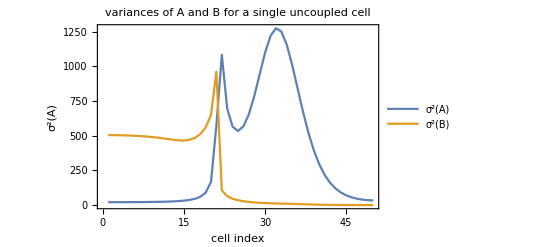

```mathematica
ListPlot[{VrA0,VrB0},Joined->{True,True,True},PlotStyle->{PointSize[0.015],Thick,Thick},Frame->True,FrameLabel->{"cell index","σ^2(A)"},PlotLegends->{"σ^2(A)","σ^2(B)"},PlotLabel->"variances of A and B for a single uncoupled cell"]
```

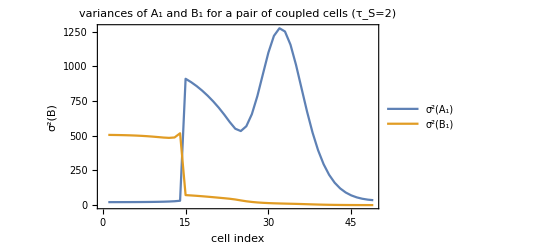

```mathematica
ListPlot[{VrA1,VrB1},Joined->{True,True,True},PlotStyle->{PointSize[0.015],Thick,Thick},Frame->True,FrameLabel->{"cell index","σ^2(B)"},PlotLegends->{"σ^2(A_1)","σ^2(B_1)"},PlotLabel->"variances of A_1 and B_1 for a pair of coupled cells (τ_S=2)"]
```

On comparing the results for the two cases, we find that there is a noticeable decrease in the variances at the boundary between A and B for the case of a pair of coupled cells. We can also visualize these results in terms of the Fano factor σ^2(X)/⟨X⟩:

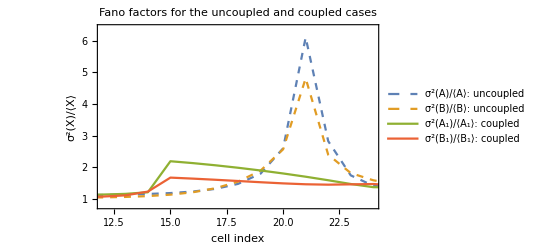

```mathematica
FA0=VrA0/X0ss[[1]]; FB0=VrB0/X0ss[[2]];
FA1=VrA1/X1ss[[1]]; FB1=VrB1/X1ss[[2]];
ListPlot[{FA0,FB0,FA1,FB1},PlotRange->{{12, 24},{0.8,6.4}},Joined->{True,True,True,True},PlotStyle->{Dashed,Dashed,Thick,Thick},Frame->True,FrameLabel->{"cell index","σ^2(X)/⟨X⟩"},PlotLegends->{"σ^2(A)/⟨A⟩: uncoupled","σ^2(B)/⟨B⟩: uncoupled","σ^2(A_1)/⟨A_1⟩: coupled","σ^2(B_1)/⟨B_1⟩: coupled"},PlotLabel->"Fano factors for the uncoupled and coupled cases"]
```